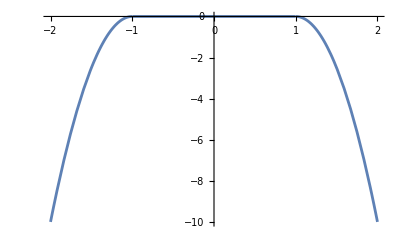

```mathematica
Estrength=0; (* Electric Force Constant *)
Rstrength=10; (* Regulation Force Constant *)

Magnitude[l_]:=Sqrt[Plus@@(l^2)];

SphereRegulationForce[p_]:=If[Magnitude[p]>=1,-Rstrength*(Magnitude[p]-1)^2, 0]
Plot[SphereRegulationForce[{0, 0, x}], {x, -2, 2}]
```

```mathematica
Eforce[p1_, p2_]:=If[p1==p2, 0*p1, Estrength*Normalize[p1-p2]/(Plus@@(p1-p2)^2)]
Eforce[{0, 0, 0}, {0, 1, 0}]
```

{0,0,0}

```mathematica
UpdateStep[pvPairs_, dt_]:=
Table[Module[{p=pvPairs[[i]][[1]], v=pvPairs[[i]][[2]]},
v=v+dt*Sum[Eforce[p,q], {q,points}];
v=v+dt*(p*SphereRegulationForce[p]);
v=v+0.001*dt*{RandomReal[], RandomReal[], RandomReal[]};
v=v+(-0.01*dt*v);
p=p+dt*v;
{p, v}
],{i, Length[pvPairs]}]
```

```mathematica
points = {{0, 0, 0}, {0, 0, 0.1}, {0, 0, 0.2}, {0, 0, 0.3}}
velocities=ConstantArray[{0, 0, 0}, Length[points]]
pv=Transpose[{points, velocities}];
pvh={};

For[i=0,i<10,i++,pvh=Join[pvh, {pv}];pv=UpdateStep[pv, 0.001]]
pv
ListPointPlot3D[pv[[All, 1]], PlotRange->All]

ph=pvh[[All, All, 1]];
```

{{0,0,0},{0,0,0.1},{0,0,0.2},{0,0,0.3}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{{2.83206×10^-8,2.66673×10^-8,3.23235×10^-8},{5.29084×10^-6,5.00678×10^-6,5.6155×10^-6}},{{2.53039×10^-8,1.60704×10^-8,0.1},{4.8691×10^-6,3.7012×10^-6,5.138×10^-6}},{{2.60709×10^-8,3.25496×10^-8,0.2},{5.50258×10^-6,5.44553×10^-6,4.73949×10^-6}},{{3.47056×10^-8,3.4011×10^-8,0.3},{5.33751×10^-6,5.01713×10^-6,5.99612×10^-6}}}

-Graphics3D-

```mathematica
ListPointPlot3D[#, PlotRange->All]&/@ph[[Range[1, Length[ph], 1]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}